```mathematica
ClearAll["Global`*"];
NotebookFind[SelectedNotebook[],"Output",All,CellStyle];FrontEndExecute[FrontEndToken["Clear"]];
NotebookDelete@Cells@MessagesNotebook[];

Get[NotebookDirectory[]<>"H2Data.m"];
Get[ParentDirectory[NotebookDirectory[]]<>"/Functions.m"];
```

Fusion rules

```mathematica
TableForm[Table[Sum[V[a,b][c]objNames[c],{c,obs}],{a,obs},{b,obs}],TableHeadings->{objNames[#]&/@obs,objNames[#]&/@obs}]
```

| 1 | α | α^2 | ρ | α ρ | α^2 ρ
1 | 1 | α | α^2 | ρ | α ρ | α^2 ρ
α | α | α^2 | 1 | α ρ | α^2 ρ | ρ
α^2 | α^2 | 1 | α | α^2 ρ | ρ | α ρ
ρ | ρ | α^2 ρ | α ρ | 1+ρ+α ρ+α^2 ρ | α^2+ρ+α ρ+α^2 ρ | α+ρ+α ρ+α^2 ρ
α ρ | α ρ | ρ | α^2 ρ | α+ρ+α ρ+α^2 ρ | 1+ρ+α ρ+α^2 ρ | α^2+ρ+α ρ+α^2 ρ
α^2 ρ | α^2 ρ | α ρ | ρ | α^2+ρ+α ρ+α^2 ρ | α+ρ+α ρ+α^2 ρ | 1+ρ+α ρ+α^2 ρ

#### Dimensions

```mathematica
dim[#]&/@obs
dtot[]^2
```

{1,1,1,1/2 (3+√13),1/2 (3+√13),1/2 (3+√13)}

3/2 (13+3 √13)

#### Frobenius-Schur indicators

```mathematica
κ[#]&/@obs
```

{1,1,1,1,1,1}

#### Unitary fusion category?

```mathematica
NpentagonQ&&NunitaryQ(*Being checked numerically, can check exactly by removing leading 'N'*)
```

True

#### Visualizations

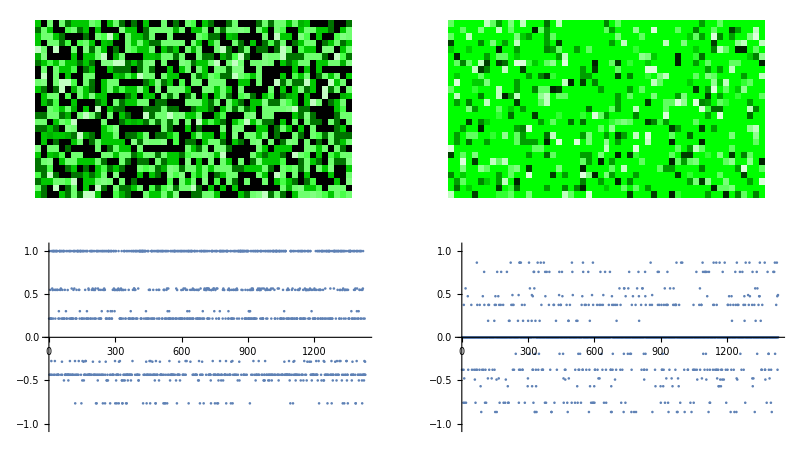

```mathematica
X=RandomSample[Fs];
GraphicsGrid[
{{ArrayPlot[ArrayReshape[(Re[X]+1)/2,{27,53},∞],ColorFunction-> (Blend[{White,Green,Black},#]&),Frame->False,ColorFunctionScaling->False],
ArrayPlot[ArrayReshape[(Im[X]+1)/2,{27,53},∞],ColorFunction-> (Blend[{White,Green,Black},#]&),Frame->False,ColorFunctionScaling->False]}
,{ListPlot[Re[X],PlotRange->{-1.05,1.05}],ListPlot[Im[X],PlotRange->{-1.05,1.05}]}}]
```

```mathematica
Fblk[3,3,3][3]//MatrixForm
```

(1/2 (-3+√13) | Root0.550Root[-1+3 #1^2+#1^4&,2]0.5502505227003375 | Root0.550Root[-1+3 #1^2+#1^4&,2]0.5502505227003375 | Root0.550Root[-1+3 #1^2+#1^4&,2]0.5502505227003375
Root0.550Root[-1+3 #1^2+#1^4&,2]0.5502505227003375 | 1/6 (7-√13) | 1/6 (1-√13) | 1/6 (1-√13)
Root0.550Root[-1+3 #1^2+#1^4&,2]0.5502505227003375 | 1/6 (1-√13) | 1/6 (1-√13) | 1/6 (7-√13)
Root0.550Root[-1+3 #1^2+#1^4&,2]0.5502505227003375 | 1/6 (1-√13) | 1/6 (7-√13) | 1/6 (1-√13))